sWLC from Li et at, 2020
Re-viewing calculation

```mathematica
(*poles of transfer functions, shared by signal and noise*)
κ=1;
γR=1;
Manipulate[ListPlot[{{Re[(-I γR+I(γR^2+4(χ^2-κ^2))^(1/2))/2],Im[(-I γR+I(γR^2+4(χ^2-κ^2))^(1/2))/2]},{Re[(-I γR-I(γR^2+4(χ^2-κ^2))^(1/2))/2],Im[(-I γR-I(γR^2+4(χ^2-κ^2))^(1/2))/2]}},PlotRange->{{-2,2},{-3,2}},AspectRatio->1,ImageSize->Small,PlotStyle->PointSize[Medium],PlotLabel->StringForm["poles of lossless transfer function\nunstable when Im[Ω]≥0\nχ/κ=``",χ/κ]],{{χ,0},0,2κ,0.1}]
```

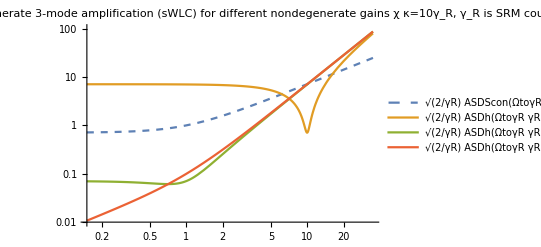
-Graphics-angular freq, Ω/γ_R / [1/γ_R]Hz (log scale)strain sensitivity (NSR), ((2 SuperscriptBox[α, 2] SubscriptBox[S, h])/γ_R)^(1/2)
/ [α/γ_R^(1/2)]Hz^(-1/2) (log scale)

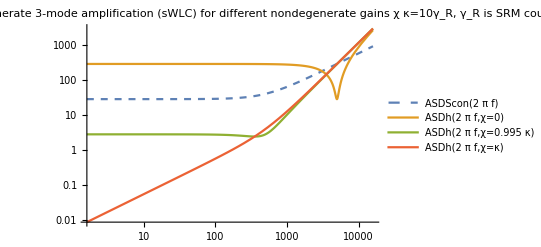
-Graphics-frequency, f=Ω/(2  π) / Hz (log scale)strain sensitivity (NSR), (α^2S_h)^(1/2)
/ [α]Hz^(-1/2) (log scale)

```mathematica
(*sensitivity curve, using values from Fig.4-5 in Li et al, 2020
they choose to plot ((2 α^2 Subscript[S, h])/Subscript[γ, R])^(1/2)*)
Clear[α,χ,κ,γR];
α=1;
γR=2π 500 (*Hz*);
κ=10γR;
Sh[Ω_,χ_]:=((Ω^2+χ^2-κ^2)^2+Ω^2 γR^2)/(4 α^2 κ^2 γR)
ASDh[Ω_,χ_]:=Abs[Sh[Ω,χ]]^(1/2)
ASDScon[Ω_]:=((Ω^2+γR^2)/(4 α^2 γR) )^(1/2)(*given*)
Labeled[LogLogPlot[{
(2/γR)^(1/2)ASDScon[ΩtoγR γR],
(2/γR)^(1/2)ASDh[ΩtoγR γR,χ=0],
(2/γR)^(1/2)ASDh[ΩtoγR γR,χ=0.995κ],
(2/γR)^(1/2)ASDh[ΩtoγR γR,χ=κ]},{ΩtoγR,0.15,35},ImageSize->400,PlotRange->{0.01,100},PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossless stable nondegenerate 3-mode amplification (sWLC)\nfor different nondegenerate gains χ\nκ=10γ_R, γ_R is SRM coupling rate",PlotStyle->{Dashed,,,}],{"angular freq, Ω/γ_R / [1/γ_R]Hz (log scale)","strain sensitivity (NSR), ((2 SuperscriptBox[α, 2] SubscriptBox[S, h])/γ_R)^(1/2)\n/ [α/γ_R^(1/2)]Hz^(-1/2) (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]
(*y-axis looks all wrong because we have scaled to α*)
Labeled[LogLogPlot[{
ASDScon[2π f],
ASDh[2π f,χ=0],
ASDh[2π f,χ=0.995κ],
ASDh[2π f,χ=κ]},{f,10/(2π),10^5/(2π)},ImageSize->400,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossless stable nondegenerate 3-mode amplification (sWLC)\nfor different nondegenerate gains χ\nκ=10γ_R, γ_R is SRM coupling rate",PlotStyle->{Dashed,,,}],{"frequency, f=Ω/(2  π) / Hz (log scale)","strain sensitivity (NSR), (α^2S_h)^(1/2)\n/ [α]Hz^(-1/2) (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]
```

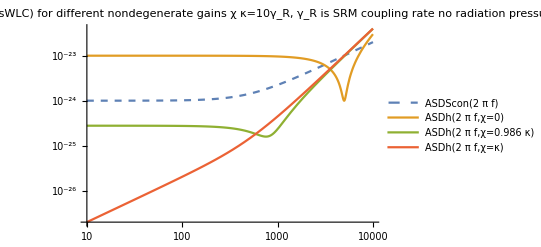
-Graphics-frequency, f=Ω/(2  π) / Hz (log scale)strain sensitivity (NSR), S_h^(1/2)
/ Hz^(-1/2) (log scale)

```mathematica
(*want to plot Sh^(1/2) against f using real values, to compare to sensitivity target
(recreating Fig.5 in Li et al, 2020 also requires radiation pressure noise, not yet derived)
This requires using the correct Subscript[α, GW] scale*)
Clear[α,χ,κ,γR];
c=3 10^8(*ms^-1*);
ℏ=1 10^-34(*Js*);
Larm=4 10^3(*m*);
Pcirc=3 10^6(*J/s*);
λ0=2 10^-6(*m*);
ω0=2π c/λ0;
(*value in Li et al doesn't make sense dimensionally, using Korobko et al 2019 instead
α=((2Pcirc ℏ ω0)/(c Larm))^(1/2);*)
α=((2Pcirc Larm ω0)/(ℏ c))^(1/2);
γR=2π 500 (*Hz*);
κ=10γR;
Labeled[LogLogPlot[{
ASDScon[2π f],
ASDh[2π f,χ=0],
ASDh[2π f,χ=0.986κ],
ASDh[2π f,χ=κ]},{f,10,10^4},ImageSize->400,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossless stable nondegenerate 3-mode amplification (sWLC)\nfor different nondegenerate gains χ\nκ=10γ_R, γ_R is SRM coupling rate\nno radiation pressure effects\nparameters of LIGO Voyager",PlotStyle->{Dashed,,,}],{"frequency, f=Ω/(2  π) / Hz (log scale)","strain sensitivity (NSR), S_h^(1/2)\n/ Hz^(-1/2) (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]
```

```mathematica
(*integrated lossless sensitivity*)
(4 α1^2 κ1^2 γR1)/(2π)Integrate[1/((Ω^2+χ1^2-κ1^2)^2+γR1^2 Ω^2),{Ω,0,∞},Assumptions->{χ1>0,κ1>0,γR1>0}]
```

ConditionalExpression[(ⅈ √2 α1^2 γR1 κ1^2)/((κ1^2-χ1^2) (√(-γR1^2+2 κ1^2-2 χ1^2+γR1 √(γR1^2-4 κ1^2+4 χ1^2))+ⅈ √(γR1^2-2 κ1^2+2 χ1^2+γR1 √(γR1^2-4 κ1^2+4 χ1^2)))),Im[√(-γR1^2+2 κ1^2-2 χ1^2-γR1 √(γR1^2-4 κ1^2+4 χ1^2))]>0&&Im[√(-γR1^2/2+κ1^2-χ1^2+1/2 γR1 √(γR1^2-4 κ1^2+4 χ1^2))]>0&&(κ1<χ1||(κ1>χ1&&2 √(κ1^2-χ1^2)≤γR1))]

Lossy sensitivity, adding loss terms to each mode, assuming each noise is quantum with uncorrelated vacuum bath

True

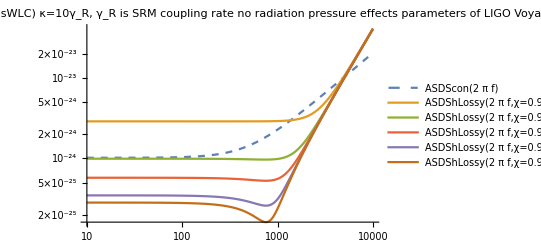
-Graphics-frequency, f=Ω/(2  π) / Hz (log scale)strain sensitivity (NSR), S_h^(1/2)
/ Hz^(-1/2) (log scale)

```mathematica
Clear[γa,γb,γc,γbtot]
ShLossy[Ω_,χ_]:=1/(4 α^2 κ^2 γR(γc^2+Ω^2))(
((γbtot-2γR)(γa γc-Ω^2)-(γa+γc)Ω^2+κ^2 γc-χ^2 γa)^2
+Ω^2(χ^2-κ^2-(γbtot-2γR)(γa+γc)-γa γc+Ω^2)^2
+4γR γa κ^2(γc^2+Ω^2)
+4γR γb(γa^2+Ω^2)(γc^2+Ω^2)
+4γR γc χ^2(γa^2+Ω^2))
ASDShLossy[Ω_,χ_,loss_]:=(ShLossy[Ω,χ]^(1/2))/.{γa->(loss γR)/(1-loss),γb->(loss γR)/(1-loss),γc->(loss γR)/(1-loss),γbtot->γR+(loss γR)/(1-loss)}
(*Checking that lossy expression can be recovered*)
losslessAsmps={γa->0,γb->0,γc->0,γbtot->γR};
((ShLossy[Ω,χ]/.losslessAsmps)==Sh[Ω,χ])//Simplify
(*Plotting*)
Labeled[LogLogPlot[{
ASDScon[2π f],
ASDShLossy[2π f,χ=0.986κ,loss=0.5],
ASDShLossy[2π f,χ=0.986κ,loss=0.1],
ASDShLossy[2π f,χ=0.986κ,loss=0.03],
ASDShLossy[2π f,χ=0.986κ,loss=0.005],
ASDShLossy[2π f,χ=0.986κ,loss=0]},{f,10,10^4},ImageSize->400,PlotLegends->LineLegend["Expressions",LabelStyle->Directive[10]],PlotLabel->"lossy stable nondegenerate 3-mode amplification (sWLC)\nκ=10γ_R, γ_R is SRM coupling rate\nno radiation pressure effects\nparameters of LIGO Voyager\nconventional detector is lossless",PlotStyle->{Dashed,,,,,}],{"frequency, f=Ω/(2  π) / Hz (log scale)","strain sensitivity (NSR), S_h^(1/2)\n/ Hz^(-1/2) (log scale)"},{Bottom,Left},RotateLabel->True,LabelStyle->Directive[10]]
```

lossless: {{Ω→1/2 ⅈ (-γR+√(γR^2-4 κ^2+4 χ^2))},{Ω→-1/2 ⅈ (γR+√(γR^2-4 κ^2+4 χ^2))}}

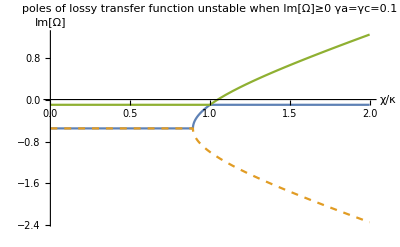

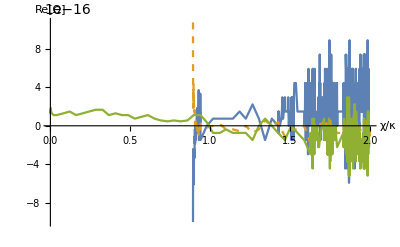

```mathematica
(*Checking stability*)
Clear[α,χ,κ,γbtot,γa,γc]
denominator=γbtot-I Ω+κ^2/(γa-I Ω)-χ^2/(γc-I Ω);
(*additional poles at γa,γc*)
Print["lossless: ",Solve[(denominator/.losslessAsmps)==0,Ω]]
sol=Simplify[Solve[denominator==0,Ω],Assumptions->{κ>0,χ>0,γa>0,γbtot>0,γc>0}];
κ=1;
γbtot=1;
γa=0.1;
γc=0.1;
(*Print["lossy: ",sol]*)
Plot[{Im[Ω/.sol[[1]]],Im[Ω/.sol[[2]]],Im[Ω/.sol[[3]]]},{χ,0,2κ},AxesLabel->{"χ/κ","Im[Ω]"},PlotLabel->"poles of lossy transfer function\nunstable when Im[Ω]≥0\nγa=γc=0.1",PlotStyle->{,Dashed,}]
Plot[{Re[Ω/.sol[[1]]],Re[Ω/.sol[[2]]],Re[Ω/.sol[[3]]]},{χ,0,2κ},AxesLabel->{"χ/κ","Re[Ω]"},PlotStyle->{,Dashed,}]
```